```mathematica
Get["G:\\Moj disk\\faks\\3. letnik 1. semester\\Napredna računalniška orodja\\mathematica\\DN 2 NRO\\mccpi.m"]
areaPi[tockevkrogu_,tockevkvadratu_]:=Module[{pivrednost,piodstopanje},pivrednost=N[4 Length[tockevkrogu]/Length[tockevkvadratu]];
piodstopanje=pivrednost-Pi;
{pivrednost,piodstopanje}]

sttock=Input["stevilo tock: "];
{tockevkrogu,tockevkvadratu}=mccpi[sttock];
{pivrednost,piodstopanje}=areaPi[tockevkrogu,tockevkvadratu];

Print["π vrednost: ",NumberForm[pivrednost,{Infinity,6}]];
Print["Odstopanje: ",NumberForm[piodstopanje,{Infinity,6}]];
```

π vrednost: 2.960000

Odstopanje: -0.181593

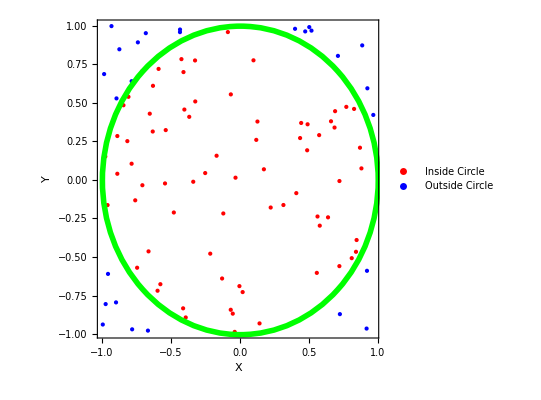

```mathematica
kroznica = Graphics[{Directive[Green, Thickness[0.01]], Circle[{0, 0}, 1]}];
tockenahrafu = ListPlot[
  {tockevkrogu, Select[tockevkvadratu, Total[#^2] > 1 &]},
  PlotStyle -> {Directive[Red, PointSize[Medium]], Directive[Blue, PointSize[Medium]]},
  PlotLegends -> {"Inside Circle", "Outside Circle"},
  AspectRatio -> 1,
  Frame -> True,
  FrameLabel -> {"X", "Y"},
  ImageSize -> 400
];

Show[tockenahrafu, kroznica]
```